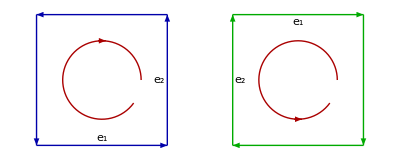

```mathematica
ClearAll[o, e1, e2, bold, sz, fs, esub, midtext, shift, sep, p1]
o = {0,0};
e2 = {0,1};
e1 = {1,0};
bold = Style[ #, Bold] &;
sz = 14;
fs = Style[ #, FontSize-> sz] &;
esub := Subscript[bold[e]// fs,#]&;
midtext[p_, sh_,text_] := Text[text,(p[[1]] + p[[2]])/2 + sh]

shift = -0.06;
sep = 1.5 e1;
r = 0.3;
p1 = Graphics[ 
{Thick,
Blue // Darker,Arrowheads[0.05],
Arrow[{{o,e1},{e1,e1+e2},{e1+e2,e2},{e2,o}}],
Black,
midtext[{o,e1} , -shift e2, esub[1] ],
midtext[{e1,e1+e2} , shift e1 , esub[2] ],
Red // Darker,
Circle[(e1+e2)/2, r,{0, 2 Pi 0.9}],
Arrow[{(e1+e2)/2 + r e2 + shift e1/2, (e1+e2)/2 + r e2 - shift e1/2}],

Green // Darker,Arrowheads[0.05],
Arrow[{
{e1 + sep,sep},
{e1+sep+e2,e1+sep},
{sep +e2,e1+sep+e2},
{sep,sep+e2}
}],
Black,

midtext[{sep +e2,e1 +sep+e2} ,+ shift e2, esub[1] ],
midtext[{sep,sep+e2} ,- shift e1, esub[2] ],

Red // Darker,
Circle[(e1+e2)/2 + sep, r,{0, 2 Pi 0.9}],
Arrow[{sep+(e1+e2)/2 - r e2 + shift e1/2, sep +(e1+e2)/2 - r e2 -shift e1/2}]
}
]
```